# Lotka Volterra ODE

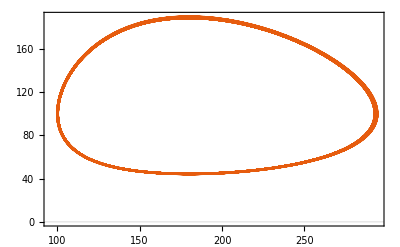

```mathematica
k1=0.1; (* 0.3 *)
k2=0.18; (* 0.6 *)
k3=0.001; (* 0.002 *)
r1=D[x[t],t]==k1*x[t]-k3*x[t]*y[t];
r2=D[y[t],t]==k3*x[t]*y[t]-k2*y[t];
initA=100;
initB=100;
tMax=2000;
sol=NDSolve[{r1,r2,x[0]==initA,y[0]==initB},{x,y},{t,0,tMax}];
data=Table[{x[t]/.sol[[1]]/.t->tVal,y[t]/.sol[[1]]/.t->tVal},{tVal,0,tMax,tMax/1000.0}];
ListLinePlot[data,PlotRange->All]
```